-Graphics3D-

(√839194)/55

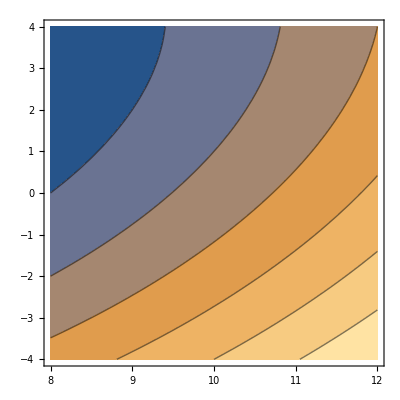

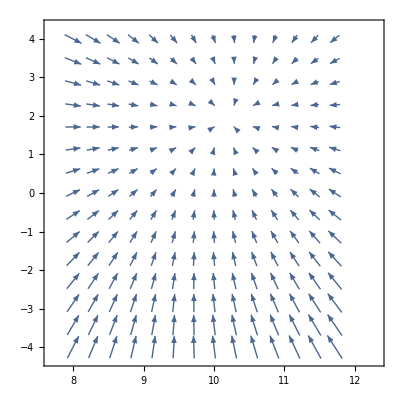

-Graphics3D-

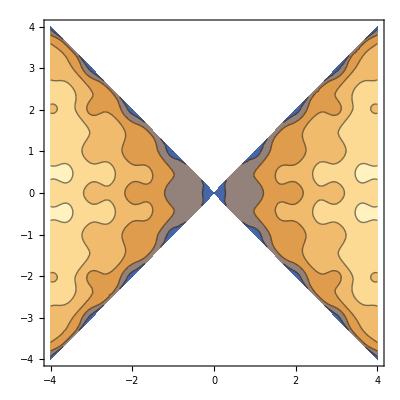

```mathematica
ClearAll["Global`*"];
F[x_, y_] := (x - 2)^2 + (y - 2)^2 - 2x*y/4;

G[x_, y_] := -20Exp[-0.2 √(0.5(x^2-y^2))]-Exp[0.5*(Cos[6.28*x]+Cos[6.28*y])]+22.71;
Plot3D[F[x, y], {x, 8, 12}, {y, -4, 4}]
h = 123123;
gradF[x_, y_] := {2(x-10) -2y/10, 2(y - 1) -2x/11};
gradFC[x_, y_, h_] := {(F[x + h, y] - F[x - h, y])/(2h), (F[x, y + h] - F[x, y - h])/(2h)};

P = {{-2, 2}, {2, 1}, {3, -1}, {-2, -2}};
eps = 0;
Do[
a = P[[i, 1]];
b = P[[i, 2]];
eps = Max[eps, Norm[gradF[a, b] - gradFC[a, b, h]]], {i, 1, 4}]
Print[eps]

ContourPlot[F[x, y], {x, 8, 12}, {y, -4, 4}]
VectorPlot[-gradF[x, y], {x, 8, 12}, {y, -4, 4}]

gradG[x_, y_] := {(G[x + h, y] - G[x - h, y])/(2h), (G[x, y + h] - G[x, y - h])/(2h)};
Plot3D[G[x, y], {x, -4, 4}, {y, -4, 4}]
ContourPlot[G[x, y], {x, -4, 4}, {y, -4, 4}]
```